# Discrete vs Mean-Field Threshold Models

## Visualization of affinity scaling results

## 1. Parameters and Core Functions

```mathematica
(* Parameters *)
γ0=1;
θ0=6;
c0=10^1;
Emax=4;
n0 = 3;

(* Hill function *)
H[x_,θ_,n_]:=x^n/(x^n+θ^n);
(* Poisson PMF *)
poiss[n_,x_]:=x^n Exp[-x]/Factorial[n];
```

```mathematica
(* Mean-field Pb *)
PbMF[EE_,n_,θ_,γ_,c_]:=1-Exp[-γ H[c (1+ⅇ^EE)^-1,θ,n]];
(* Discrete Hill Pb (truncated sum) *)
PbDisc[EE_,n_,θ_,γ_,c_,kmax_:20]:=Module[{π=c (1+ⅇ^EE)^-1},1-Sum[poiss[k,π](Exp[-γ H[k,θ,n]]),{k,0,kmax}]];
(* Discrete sharp threshold Pb *)
PbSharp[EE_,θ_,γ_,c_,kmax_:40]:=Module[{π=c (1+ⅇ^EE)^-1},(1-Exp[-γ])*(Sum[poiss[k,π],{k,θ,kmax}])];
```

## 2. Main Comparison: Mean-Field vs Discrete Hill vs Sharp Threshold

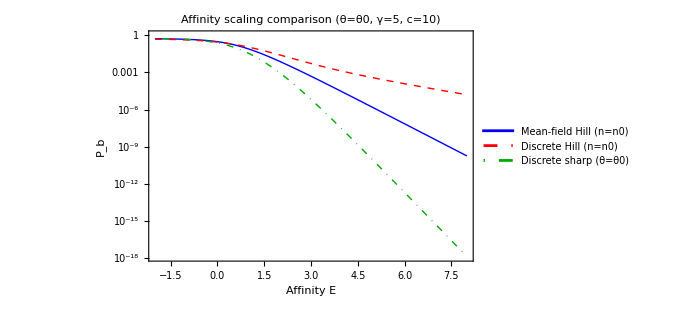

```mathematica
LogPlot[Evaluate[{PbMF[EE,n0,θ0,γ0,c0],PbDisc[EE,n0,θ0,γ0,c0],PbSharp[EE,θ0,γ0,c0]}],{EE,-2,Emax+4},
PlotStyle->{{Blue,Thick},{Red,Thick,Dashed},{Darker[Green],Thick,DotDashed}},
PlotLegends->{"Mean-field Hill (n=n0)","Discrete Hill (n=n0)","Discrete sharp (θ=θ0)"},
AxesLabel->{"E","P_b"},PlotLabel->"Affinity scaling comparison (θ=θ0, γ=5, c=10)",
PlotRange->Automatic,ImageSize->500,Frame->True,FrameLabel->{"Affinity E","P_b"}]
```

## 3. Slope Comparison: Effective Exponent

```mathematica
(* Local slope = -d log(Pb)/dE *)
slopeMF[EE_]:=-D[Log[PbMF[e,n0,θ0,γ0,c0]],e]
slopeDisc[EE_]:=-(Log[PbDisc[EE+0.001,n0,θ0,γ0,c0]]-Log[PbDisc[EE,n0,θ0,γ0,c0]])/0.001;
slopeSharp[EE_]:=-(Log[PbSharp[EE+0.001,θ0,γ0,c0]]-Log[PbSharp[EE,θ0,γ0,c0]])/0.001;
```

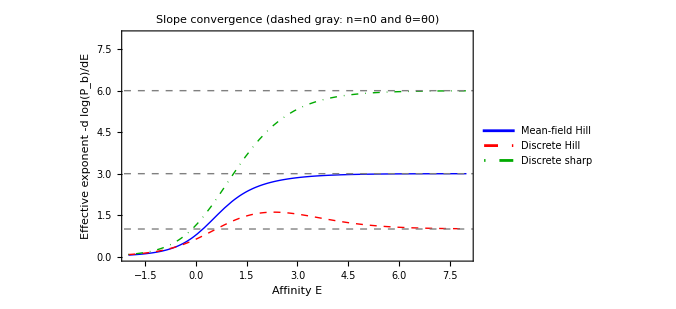

```mathematica
Plot[{slopeMF[EE]/.e->EE,slopeDisc[EE],slopeSharp[EE]},{EE,-2,Emax+4},
PlotStyle->{{Blue,Thick},{Red,Thick,Dashed},{Darker[Green],Thick,DotDashed}},
PlotLegends->{"Mean-field Hill","Discrete Hill","Discrete sharp"},
Epilog->{Dashed,Gray,InfiniteLine[{0,n0},{1,0}],InfiniteLine[{0,1},{1,0}],InfiniteLine[{0,θ0},{1,0}]},
Frame->True,FrameLabel->{"Affinity E","Effective exponent  -d log(P_b)/dE"},PlotLabel->"Slope convergence (dashed gray: n=n0 and θ=θ0)",
ImageSize->500,PlotRange->{0,θ0+2}]
```

## 4. Convergence: Discrete Hill → Sharp Threshold as n → ∞

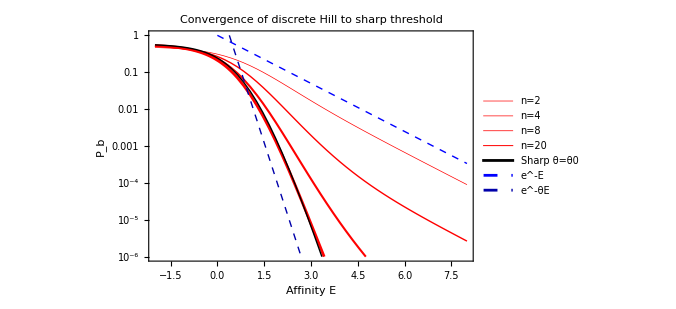

```mathematica
LogPlot[Evaluate[Join[Table[PbDisc[EE,n,θ0,γ0,c0],{n,{2,4,8,20}}],{PbSharp[EE,θ0,γ0,c0], Exp[-EE], 10Exp[-θ0*EE]}]],{EE,-2,Emax+4},
PlotStyle->{{Red,Thickness[0.001]},{Red,Thickness[0.002]},{Red,Thickness[0.003]},{Red,Thickness[0.004]},{Black,Thick},{Blue,Thick, Dashed},{Darker[Blue],Thick, Dashed}},
PlotLegends->{"n=2","n=4","n=8","n=20","Sharp θ=θ0", "e^-E", "e^-θE"},
PlotRange->{10^-6,1},Frame->True,FrameLabel->{"Affinity E","P_b"},
PlotLabel->"Convergence of discrete Hill to sharp threshold",ImageSize->500]
```

## 5. Non-Commutativity: Crossover Scale

```mathematica
(* Show the k=1 and k=θ contributions separately *)
term1[EE_,n_]:=Module[{π=c0 ⅇ^-EE},poiss[1,π](1-Exp[-γ0 H[1,θ0,n]])];
termTheta[EE_,n_]:=Module[{π=c0 ⅇ^-EE},poiss[θ0,π](1-Exp[-γ0 H[θ0,θ0,n]])];
```

```mathematica
Manipulate[
LogPlot[{term1[EE,n],termTheta[EE,n],PbDisc[EE,n,θ0,γ0,c0]},{EE,0,Emax+6},
PlotStyle->{{Orange,Dashed},{Purple,Dashed},{Black,Thick}},
PlotLegends->{"k=1 term (∝ ⅇ^-E)","k=θ term (∝ ⅇ^-θE)","Full P_b"},
PlotRange->{10^-16,1},Frame->True,FrameLabel->{"E","Contribution to P_b"},
PlotLabel->Row[{"Crossover between k=1 and k=θ channels, n=",n}],
Epilog->{Gray,Dashed, InfiniteLine[{Log[(c0*θ0^(n/(θ0-1))-1)],0},{0,1}]},ImageSize->500],
{{n,4,"Hill coefficient n"},{2,4,8,12,20}}]
```

## 6. Reference Slopes Overlay

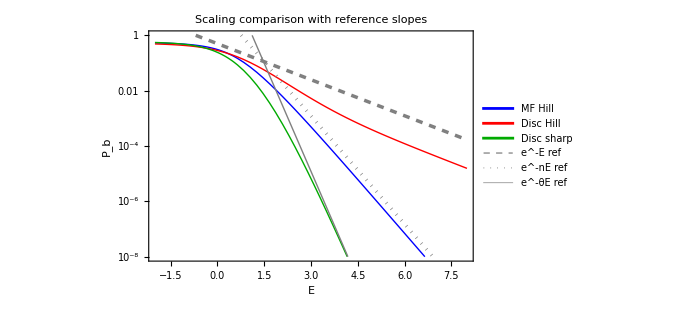

```mathematica
LogPlot[{PbMF[EE,n0,θ0,γ0,c0],PbDisc[EE,n0,θ0,γ0,c0],PbSharp[EE,θ0,γ0,c0],
(* Reference lines *)
.5 ⅇ^-EE,10 ⅇ^(-n0 EE),800 ⅇ^(-θ0 EE)},{EE,-2,Emax+4},
PlotStyle->{{Blue,Thick},{Red,Thick},{Darker[Green],Thick},{Gray,Thickness[.005],Dashed},{Gray,Thickness[.005],Dotted},{Gray,Thickness[.002],Solid}},
PlotLegends->{"MF Hill","Disc Hill","Disc sharp","e^-E ref","e^-nE ref","e^-θE ref"},
PlotRange->{10^-8,1},Frame->True,FrameLabel->{"E","P_b"},
PlotLabel->"Scaling comparison with reference slopes",ImageSize->500]
```